```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumObject[f,g,γ1,γ2];
```

```mathematica
Do[⟦γ1[i],γ1[j]⟧_+=2*KroneckerDelta[i,j],{i,0,7},{j,0,7}]
```

```mathematica
Do[⟦γ2[i],γ2[j]⟧_+=2*KroneckerDelta[i,j],{i,0,7},{j,0,7}]
```

```mathematica
Do[⟦γ1[i],γ2[j]⟧_+=0,{i,0,7},{j,0,7}]
```

```mathematica
Do[γ1[i]^2=1,{i,0,7}]
```

```mathematica
Do[γ2[i]^2=1,{i,0,7}]
```

```mathematica
f2m=Flatten[Table[{f[i]->(γ1[i]-I γ2[i])/2,SuperDagger[f[i]]->(γ1[i]+I γ2[i])/2},{i,0,7}]]
```

{f[0]→1/2 (γ1[0]-ⅈ γ2[0]),f[0]^†→1/2 (γ1[0]+ⅈ γ2[0]),f[1]→1/2 (γ1[1]-ⅈ γ2[1]),f[1]^†→1/2 (γ1[1]+ⅈ γ2[1]),f[2]→1/2 (γ1[2]-ⅈ γ2[2]),f[2]^†→1/2 (γ1[2]+ⅈ γ2[2]),f[3]→1/2 (γ1[3]-ⅈ γ2[3]),f[3]^†→1/2 (γ1[3]+ⅈ γ2[3]),f[4]→1/2 (γ1[4]-ⅈ γ2[4]),f[4]^†→1/2 (γ1[4]+ⅈ γ2[4]),f[5]→1/2 (γ1[5]-ⅈ γ2[5]),f[5]^†→1/2 (γ1[5]+ⅈ γ2[5]),f[6]→1/2 (γ1[6]-ⅈ γ2[6]),f[6]^†→1/2 (γ1[6]+ⅈ γ2[6]),f[7]→1/2 (γ1[7]-ⅈ γ2[7]),f[7]^†→1/2 (γ1[7]+ⅈ γ2[7])}

```mathematica
t*(SuperDagger[f[0]]·f[1]+SuperDagger[f[1]]·f[0])+Δ*(f[0]·f[1]+SuperDagger[f[1]]·SuperDagger[f[0]])/.f2m//Simplify
```

1/2 ⅈ ((t+Δ) γ2[1]·γ1[0]+(t-Δ) γ2[0]·γ1[1])

```mathematica
f[0]·f[1]+SuperDagger[f[1]]·SuperDagger[f[0]]/.f2m//Simplify
```

1/2 ⅈ (γ2[1]·γ1[0]+γ1[1]·γ2[0])

```mathematica
PauliMatrix[1].PauliMatrix[3]
```

{{0,-1},{1,0}}

```mathematica
I*PauliMatrix[2]
```

{{0,1},{-1,0}}

```mathematica
z1=SparseArray[{{1,1}->1,{2,2}->1,{3,4}->-1,{4,3}->1}]
```

SparseArray[…]

```mathematica
Inverse@z1
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,-1,0}}

```mathematica
sp=(PauliMatrix[1]+I*PauliMatrix[2])/2
```

{{0,1},{0,0}}

```mathematica
sm=(PauliMatrix[1]-I*PauliMatrix[2])/2
```

{{0,0},{1,0}}

```mathematica
sm.PauliMatrix[3]
```

{{0,0},{1,0}}

```mathematica
PauliMatrix[3].sm
```

{{0,0},{-1,0}}

```mathematica
(PauliMatrix[1].sp+PauliMatrix[1]).{0,1}
```

{1,1}

```mathematica
PauliMatrix[3].sp
```

{{0,1},{0,0}}

```mathematica
-sp.PauliMatrix[3]
```

{{0,1},{0,0}}

```mathematica
D[(h-Cos[α])^2+γ2*Sin[α]^2,α]
```

2 (h-Cos[α]) Sin[α]+2 γ2 Cos[α] Sin[α]

```mathematica
γ2
```

γ2

```mathematica
min[h_,γ_]:=Block[{cand},cand=If[Abs[γ^2+h]≤1,{0,π,ArcCos[γ^2+h]},{0,π}];Min[(h-Cos[α])^2+γ^2*Sin[α]^2/.α->cand]]
```

```mathematica
min[1,0]
```

0

```mathematica
data=Table[min[h0,γ0],{h0,0,2,.01},{γ0,0,2,.01}];
```

```mathematica
ArrayPlot[Reverse@Log@data,DataRange->{{0,2},{0,2}},FrameTicks->True,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Table[Block[{h=h0,γ=γ0},Minimize[(h-Cos[α])^2+γ^2*Sin[α]^2,α]][[1]],{h0,0,2,.2},{γ0,0,2,.2}]
```

{{3.7494×10^-33,0.04,0.16,0.36,0.64,1.,1.,1.,1.,1.,1.},{6.93335×10^-33,0.0383333,0.152381,0.3375,0.568889,0.64,0.64,0.64,0.64,0.64,0.64},{3.08149×10^-33,0.0333333,0.129524,0.27,0.36,0.36,0.36,0.36,0.36,0.36,0.36},{0.,0.025,0.0914286,0.1575,0.16,0.16,0.16,0.16,0.16,0.16,0.16},{0.,0.0133333,0.0380952,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04},{1.2326×10^-32,9.50663×10^-37,1.64101×10^-37,3.18666×10^-38,1.41438×10^-39,4.72183×10^-39,2.49417×10^-38,5.639×10^-38,9.65293×10^-38,1.44271×10^-37,1.99072×10^-37},{0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04},{0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16,0.16},{0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36},{0.64,0.64,0.64,0.64,0.64,0.64,0.64,0.64,0.64,0.64,0.64},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

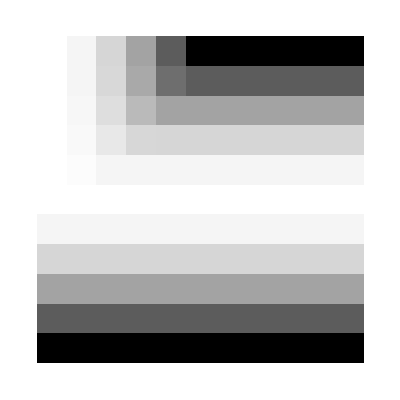

```mathematica
ArrayPlot@%
```

```mathematica
sm.sp-sp.sm
```

{{-1,0},{0,1}}

```mathematica
PauliMatrix[3].sp-sp.PauliMatrix[3]
```

{{0,2},{0,0}}

```mathematica
PauliMatrix[3].sm-sm.PauliMatrix[3]
```

{{0,0},{-2,0}}

```mathematica
sm.PauliMatrix[3]
```

{{0,0},{1,0}}

```mathematica
PauliMatrix[3].sm
```

{{0,0},{-1,0}}

```mathematica
PauliMatrix[3].
```

```mathematica
σ
```